```mathematica
Figure 4: (A-D) Treatment protocol modification: Single additional dose given at a prescribed day
A -  Cartoon schematic showing the additional dose window (not done in mathematica).
B - Typical patient treatment window for representative patients with different growth rates.
C- Typical patient treatment window for representative patients with different initial tumor sizes.
C - Relative survival improvement over the baseline of the patient (PFS[two doses]/PFS[one dose]) with an additional dose at day 100.
D - Array plot showing treatment window as a function of initial tumor size and memory fraction at infusion.
E - ?????
F - ?????
```

```mathematica
Fig 4b: Representative patients for the sliding treatment window
```

1000

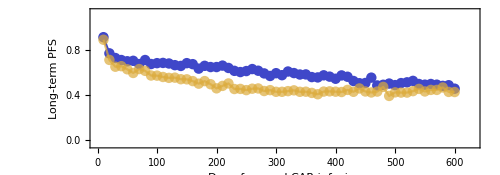

/Users/altrock/Dropbox/Projects_Dropbox/CART/code/hybridModelRuns/TreatmentWindow_varyrB.pdf

```mathematica
(* This module creates a K-M curve using the given filename *)
dir=NotebookDirectory[]<>"additionalDose/";
makeSurvivalCurve[filename_]:=Module[
{data,patients,time,ci,S},
data=Import[dir<>filename,"Data"];
patients = data[[4;;]]; (* The first 3 lines contain parameter info *)
time={};
(* We now loop over all patients and look to see when progression occurs (we add large number to cure so it will never show progression in the K-M curve). *)
For[n=1,n≤ Length[patients],n++,
If[patients[[n,2]]=="cure",AppendTo[time,patients[[n,1]]+10000],AppendTo[time,patients[[n,1]]]]];
ci=0&/@Range[Length[time]];
S=SurvivalModelFit[EventData[time,ci]];
{time,ci,patients,S}
]
cureRate[file_]:= Module[
{data,patients,cureTimes,progressionTimes},
data=Import[dir<>file,"Data"];
patients=data[[4;;]];
cureTimes = {};
progressionTimes={};
For[n=1,n≤Length[patients],n++,
If[patients[[n,2]]=="cure",AppendTo[cureTimes,patients[[n,1]]],AppendTo[progressionTimes,patients[[n,1]]]]];
{cureTimes//Length,progressionTimes//Length}
]
parentString="outputData_chemoOn_";
extensionString = "_2019-11-21.txt";
nInitFile=1;
nFiles=60;
nTotFiles = 180;
listOfFiles=parentString<>ToString[#]<>extensionString&/@Range[nInitFile,nTotFiles];
(*sFine=cureRate[listOfFiles[[#]]]&/@Range[1,nFiles];*)
sAllrB = Table[Table[cureRate[listOfFiles[[n]]],{n,1+nFiles m,nFiles(1+m)}],{m,0,nTotFiles/nFiles-1}];

lgrB = ("r_B = "<>ToString[0.065+0.05#]<>"/day")&/@Range[0,2];
Tf=600;
nPatients=1000
L1[i_,c_]:=ListPlot[Table[{10n,sAllrB[[i,n,1]]/nPatients},{n,1,nFiles}],
PlotRange->{{0,1.05}Tf,{-0.05,1.15}},
(*GridLines->{{},{1.0}},*)
FrameLabel->{"Day of second CAR infusion","Long-term PFS"},
FrameStyle->Directive[Thickness[0.0025],Black],
Frame->{{True,False},{True,False}},
Joined->True,
Mesh->All,
(*PlotMarkers->{Automatic},*)
PlotStyle->Directive[c,PointSize->0.015],
PlotLegends->Placed[SwatchLegend[{lgrB[[i]]},LegendMarkerSize->10,LegendMarkers->"Bubble"],{0.65,0.9}],
LabelStyle->{Black,FontSize->18,FontFamily->"Arial"},
ImageSize->500,
AspectRatio->0.35
];

(*Show[L1[#,ColorData["Rainbow"][(Mod[#,3]+1)/3]]&/@Range[4,12,8]]*)
fig4a=Show[L1[1,ColorData["Rainbow"][0.15]](*,L1[2,ColorData["Rainbow"][0.45]]*),L1[3,Opacity[0.7,ColorData["Rainbow"][0.75]]]]
Export[NotebookDirectory[]<>"TreatmentWindow_varyrB.pdf",fig4a,"PDF"]
```

```mathematica
dir=NotebookDirectory[]<>"additionalDose/";
makeSurvivalCurve[filename_]:=Module[
{data,patients,time,ci,S},
data=Import[dir<>filename,"Data"];
patients = data[[4;;]]; (* The first 3 lines contain parameter info *)
time={};
(* We now loop over all patients and look to see when progression occurs (we add large number to cure so it will never show progression in the K-M curve). *)
For[n=1,n≤ Length[patients],n++,
If[patients[[n,2]]=="cure",AppendTo[time,patients[[n,1]]+10000],AppendTo[time,patients[[n,1]]]]];
ci=0&/@Range[Length[time]];
S=SurvivalModelFit[EventData[time,ci]];
{time,ci,patients,S}
]
cureRate[file_]:= Module[
{data,patients,cureTimes,progressionTimes},
data=Import[dir<>file,"Data"];
patients=data[[4;;]];
cureTimes = {};
progressionTimes={};
For[n=1,n≤Length[patients],n++,
If[patients[[n,2]]=="cure",AppendTo[cureTimes,patients[[n,1]]],AppendTo[progressionTimes,patients[[n,1]]]]];
{cureTimes//Length,progressionTimes//Length}
]
parentString="outputData_chemoOn_";
extensionString = "_2019-11-22.txt";
nInitFile=1;
nFiles=60;
nTotFiles = 360;
listOfFiles=parentString<>ToString[#]<>extensionString&/@Range[nInitFile,nTotFiles];
(*sFine=cureRate[listOfFiles[[#]]]&/@Range[1,nFiles];*)
sAllB0= Table[Table[cureRate[listOfFiles[[n]]],{n,1+nFiles m,nFiles(1+m)}],{m,0,nTotFiles/nFiles-1}];
```

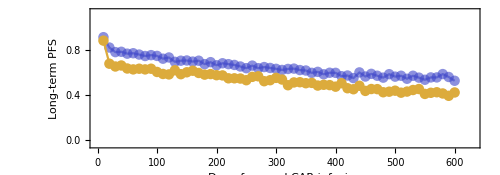

Show::gcomb: Could not combine the graphics objects in Show[L2[1,Opacity[0.6,RGBColor[0.2480688, 0.2797284, 0.7879248]]],L2[6,RGBColor[0.863512, 0.670771, 0.236564]]].

Show[L2[1,Opacity[0.6,RGBColor[0.2480688, 0.2797284, 0.7879248]]],L2[6,RGBColor[0.863512, 0.670771, 0.236564]]]

```mathematica
lgB0 =( "B_0 = "<>ToString[Round[# 200,1]]<>" cm^3")&/@{0.01,0.1,1.0,2.0,5.0,10.0};
Tf=600;
L2[i_,c_]:=ListPlot[Table[{10n,sAllB0[[i,n,1]]/1000},{n,1,nFiles}],
PlotRange->{{0,1.05}Tf,{-0.05,1.15}},
(*GridLines->{{},{1.0}},*)
FrameLabel->{"Day of second CAR infusion","Long-term PFS"},
FrameStyle->Directive[Thickness[0.0025],Black],
Frame->{{True,False},{True,False}},
Joined->True,
Mesh->All,
(*PlotMarkers->{Automatic},*)
PlotStyle->Directive[c,PointSize->0.015],
PlotLegends->Placed[SwatchLegend[{lgB0[[i]]},LegendMarkerSize->10,LegendMarkers->"Bubble"],{0.65,0.9}],
LabelStyle->{Black,FontSize->18,FontFamily->"Arial"},
(*GridLines->{{},{0.48}},*)
ImageSize->500,
AspectRatio->0.35
];

fig4b=Show[L2[1,Opacity[0.6,ColorData["Rainbow"][0.15]]](*,L2[3,ColorData["Rainbow"][0.45]]*),L2[6,ColorData["Rainbow"][0.75]]]
```

```mathematica
Export[NotebookDirectory[]<>"TreatmentWindow_varyB0.pdf",fig4b,"PDF"]
```

/Users/gregorykimmel/Dropbox/_Projects/01_CART/code/hybridModelRuns/TreatmentWindow_varyB0.pdf

```mathematica
(* This module creates a K-M curve using the given filename *)
dirAddDose=NotebookDirectory[]<>"additionalDose/";
dirBaseline=NotebookDirectory[]<>"runData/";
makeSurvivalCurve[filename_,direct_]:=Module[
{data,patients,time,ci,S},
data=Import[direct<>filename,"Data"];
patients = data[[4;;]]; (* The first 3 lines contain parameter info *)
time={};
(* We now loop over all patients and look to see when progression occurs (we add large number to cure so it will never show progression in the K-M curve). *)
For[n=1,n≤ Length[patients],n++,
If[patients[[n,2]]=="cure",AppendTo[time,patients[[n,1]]+10000],AppendTo[time,patients[[n,1]]]]];
ci=0&/@Range[Length[time]];
S=SurvivalModelFit[EventData[time,ci]];
{time,ci,patients,S}
];
```

```mathematica
nInitFile=1;
nEndFile=42;
nFiles = nEndFile-nInitFile+1;
extensionString = "_2019-11-25.txt";
tablePercentImprove=makeSurvivalCurve["outputData_chemoOn_"<>ToString[#]<>extensionString,dirAddDose]⟦4⟧&/@Range[1,nFiles];
tablePercentBaseline=makeSurvivalCurve["outputData_"<>ToString[#]<>extensionString,dirBaseline]⟦4⟧&/@Range[1,nFiles];
```

```mathematica
(* We loop through B0 and rB *)
rB=0.04+0.025#&/@Range[0,6];
B0={0.01,0.1,1.0,2.0,5.0,10.0};
```

```mathematica
tablePercentImprove[[#]][200]/tablePercentBaseline[[#]][200]&/@Range[1,nFiles]-1
```

{0.0362694,0.144186,0.29364,0.345753,0.40228,0.394046,0.40619,0.0449791,0.175981,0.292517,0.409302,0.379368,0.614286,0.562633,0.0562036,0.183353,0.303244,0.349454,0.587121,0.56701,0.543046,0.05074,0.162455,0.292373,0.338118,0.468864,0.39726,0.516411,0.0923603,0.197875,0.287926,0.393673,0.426531,0.372385,0.466346,0.118471,0.127721,0.226351,0.310078,0.269474,0.301149,0.335079}

```mathematica
relativeImprove=ArrayReshape[tablePercentImprove[[#]][200]/tablePercentBaseline[[#]][200]&/@Range[1,nFiles]-1,{B0//Length,rB//Length}]//Transpose
```

{{0.0362694,0.0449791,0.0562036,0.05074,0.0923603,0.118471},{0.144186,0.175981,0.183353,0.162455,0.197875,0.127721},{0.29364,0.292517,0.303244,0.292373,0.287926,0.226351},{0.345753,0.409302,0.349454,0.338118,0.393673,0.310078},{0.40228,0.379368,0.587121,0.468864,0.426531,0.269474},{0.394046,0.614286,0.56701,0.39726,0.372385,0.301149},{0.40619,0.562633,0.543046,0.516411,0.466346,0.335079}}

```mathematica
test=RandomReal[{0,1},12]
```

{0.48846,0.0011156,0.716417,0.968,0.105404,0.711625,0.384759,0.468087,0.712467,0.365661,0.112025,0.604712}

```mathematica
ArrayReshape[test,{4,3}]//MatrixForm
```

(0.855681 | 0.809124 | 0.771907
0.767088 | 0.922696 | 0.15232
0.0659127 | 0.699879 | 0.225817
0.17958 | 0.37941 | 0.59967)

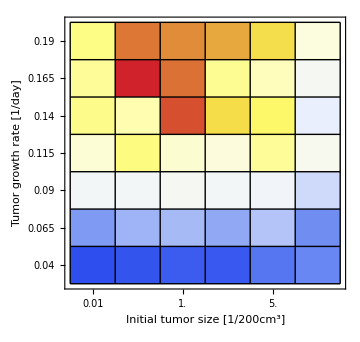

```mathematica
fig4d=ArrayPlot[relativeImprove
,ColorFunction->"TemperatureMap"
,ColorFunctionScaling->True
,Background->White
,Frame->True
,AspectRatio->0.95
,ImageSize->360
,LabelStyle->{Black,FontSize->18,FontFamily->"Arial"}
,FrameStyle->Directive[Thickness[0.0035],Black]
,LabelStyle->{FontSize->24,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
, FrameLabel -> {{"Initial tumor size [1/200cm^3]",None},{"Tumor growth rate [1/day]",(*"Percent improvenment in PFS"*)None}}
,FrameTicks->{
{#,ToString[rB[[#]]]}&/@Range[rB//Length],
{#,ToString[B0[[#]]]}&/@Range[B0//Length]
}
(*,PlotLegends->Automatic*)
,Mesh->All
,MeshStyle->Black
,DataReversed->{True,False}
,PlotLegends->{Placed[BarLegend[{"TemperatureMap",{Min[relativeImprove]100,Max[relativeImprove]100}}],Bottom]}
]
```

```mathematica
Export[NotebookDirectory[]<>"relativeImprovement_rB_vs_B0.pdf",fig4d,"PDF"]
```

/Users/gregorykimmel/Dropbox/_Projects/01_CART/code/hybridModelRuns/relativeImprovement_rB_vs_B0.pdf

```mathematica
Max[relativeImprove]
Min[relativeImprove]
```

0.614286

0.0362694